## New Boson - Excitation Energies

```mathematica
ClearAll["Global`*"]
```

```mathematica
exportPrePathMacMini="/Users/basavyr/Offline-Work/Repos/phdthesis/Chapters/Figures";
exportPrePathMacBook="/Users/basavyr/Documents/Work/PhD/phdthesis/Chapters/Figures";
exportPrePath="";
isSystemMacBook=ContainsAny[{"MacBook"},StringSplit[StringTemplate["``"][$MachineName],"-"]];
If[isSystemMacBook,exportPrePath=exportPrePathMacBook,exportPrePath=exportPrePathMacMini];
```

```mathematica
export[object_,name_]:=Export[StringTemplate["``/``.pdf"][exportPrePath,name],object, ImageResolution->1500];
```

```mathematica
A={1/(2*91),1/(2*9),1/(2*51)};
j=11/2;
I0=11/2;
thetarad=-119*π/180;
j1=j*Cos[thetarad];
j2=j*Sin[thetarad];
```

Analytical formulas - E

```mathematica
omega[I_]:=(((2I+1)(A[[2]]-A[[1]]-(A[[2]]j2)/I)+2A[[1]]j1)*((2I+1)(A[[3]]-A[[1]])+2A[[1]]j1)-(A[[3]]-A[[1]])(A[[2]]-A[[1]]-(A[[2]]*j2)/I))^(1/2);
hmin[I_]:=A[[1]] I^2-(2I+1)A[[1]]j1-I*A[[2]]j2+A[[1]] j1^2+A[[2]] j2^2;
EnergyAbs[I_,n_]:=hmin[I-n]+omega[I-n](n+1/2);
EnergyExc[I_,n_]:=EnergyAbs[I,n]-EnergyAbs[I0,0];
```

Analytical formulas - E’

```mathematica
omegaprime[I_]:=(((2I+1)(A[[2]]-A[[1]]-(A[[2]]j2)/I)-2A[[1]]j1)*((2I+1)(A[[3]]-A[[1]])-2A[[1]]j1)-(A[[3]]-A[[1]])(A[[2]]-A[[1]]-(A[[2]]j2)/I))^(1/2);
hminprime[I_]:=A[[1]] I^2+(2I+1)A[[1]]j1-I*A[[2]]j2+A[[1]] j1^2+A[[2]] j2^2;
EnergyAbsPrime[I_,n_]:=hminprime[I-n]+omegaprime[I-n](n+1/2);
EnergyExcPrime[I_,n_]:=EnergyAbsPrime[I,n]-EnergyAbsPrime[I0,0];
```

Theoretical data

```mathematica
spins1=Table[i,{i,5.5,27.5,2}];
spins2=Table[i,{i,8.5,16.5,2}];
spins3=Table[i,{i,9.5,15.5,2}];
```

```mathematica
band1=Map[SetPrecision[EnergyExc[#,0],4]&,spins1];
band1Prime=Map[SetPrecision[EnergyExcPrime[#,0],4]&,spins1];
band2=Map[SetPrecision[EnergyExc[#,0],4]&,spins2];
band2Prime=Map[SetPrecision[EnergyExcPrime[#,0],4]&,spins2];
band3=Map[SetPrecision[EnergyExc[#,1],4]&,spins3];
band3Prime=Map[SetPrecision[EnergyExcPrime[#,1],4]&,spins3];
```

```mathematica
Print["B1\n",spins1,"\n",band1,"\n",band1Prime]
```

B1
{5.5,7.5,9.5,11.5,13.5,15.5,17.5,19.5,21.5,23.5,25.5,27.5}
{-2.776×10^-17,0.7711,1.584,2.439,3.337,4.28,5.265,6.295,7.369,8.486,9.647,10.85}
{-5.274×10^-16,0.6476,1.339,2.075,2.855,3.679,4.547,5.458,6.414,7.414,8.458,9.545}

```mathematica
Print["B2\n",spins2,"\n",band2,"\n",band2Prime]
```

B2
{8.5,10.5,12.5,14.5,16.5}
{1.172,2.006,2.883,3.803,4.767}
{0.9879,1.702,2.46,3.261,4.107}

```mathematica
Print["B3\n",spins3,"\n",band3,"\n",band3Prime]
```

B3
{9.5,11.5,13.5,15.5}
{1.435,2.332,3.271,4.253}
{1.387,2.159,2.976,3.836}

Experimental data

```mathematica
gamma1Exp={372.9,659.8,854.3,999.7,1075.6,843.7,834.3,882.2,922.4,957.0,1005};
gamma2Exp={726.5,795.7,955.7,1111.7};
gamma3Exp={826.3,763.8,1009.0};
```

Experimental energies for the three bands, taking the numerical results from the CPP code (see this repository: https://github.com/basavyr/pr135_EnergyFit_TW1TW2/blob/a1ce719a2630e0ee3a7f4fee7d507b1c32faba26/include/expdata.h#L23)

The bands B2 and B3 are normalized to the ground band of B1, ignoring the transition γ(15/2^-->11/2^-)

Technically the normalization must include the true difference, which consists of the γ(17/2^-->15/2^-) + γ(15/2^-->11/2^-) for B2 and γ(19/2^-->15/2^-) + γ(15/2^-->11/2^-) for B3

Check the following scheme:-Graphics-

```mathematica
(*taken from the C++ 2020-implementation - DOES NOT CONSIDER transition γ(15/2^-->11/2^-)= *)
e01CPP=358.0; 
e02CPP=358.0+746.6;
e03CPP=358.0+1197.1;
```

```mathematica
(*taken from the 2023-Python implementation - TAKES transition γ(15/2^-->11/2^-) *)
e01=358.0;
e02=358.0+372.9+1477.9;
e03=358.0+272.9+1197.1;
```

```mathematica
band1Exp={0.0,0.3729,1.0327,1.887,2.8867,3.9623,4.806,5.6403,6.5225,7.4449,8.4019,9.4069};
band1ExpCPP={0.0,0.3729,1.0327,1.887,2.8867,3.9623,4.806,5.6403,6.5225,7.4449,8.4019,9.4069};
band2Exp={1.1195,1.846,2.6417,3.5974,4.7091};
band2ExpCPP={0.7466,1.4731,2.2688,3.2245,4.3362};
band3Exp={1.57,2.3963,3.1601,4.1691};
band3ExpCPP={1.1971,2.0234,2.7872,3.7962};
```

```mathematica
f1=ListPlot[{Table[{spins1[[i]],band1Prime[[i]]},{i,2,Length[spins1]}],Table[{spins1[[i]],band1ExpCPP[[i]]},{i,2,Length[band1Exp]}]},Joined->{True,False},PlotStyle->{{Red,Thick},{Black}},AspectRatio->0.85,FrameStyle->Directive[Black,Thick]];
```

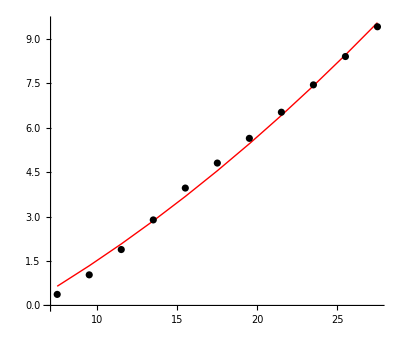

```mathematica
Show[f1]
```